## State

```mathematica
SetDirectory[NotebookDirectory[]];
<<ArmaBinary`
Run["./run"];
MatrixForm[w=ImportArmaBinary["w.bin"][[1]]];
MatrixForm[w0=ImportArmaBinary["w0.bin"][[1]]];
MatrixForm[psi=ImportArmaBinary["psi.bin"]];
```

```mathematica
L=10;t1=0.3;t2=1.;t3=0.2;t4=0.9;dmu=+0.2;
w=ImportArmaBinary["w.bin"][[1]];
w1=Flatten[Table[
kx=2.Pi i/L;ky=2.Pi j/L;
Eigenvalues[{
{-2t1 Cos[ky]-2t4 Cos[kx]-1/2dmu,-4t2 Cos[kx/2]Cos[ky/2]-4t3(Cos[kx/2]Cos[3ky/2]+Cos[3kx/2]Cos[ky/2])},
{-4t2 Cos[kx/2]Cos[ky/2]-4t3(Cos[kx/2]Cos[3ky/2]+Cos[3kx/2]Cos[ky/2]),-2t1 Cos[kx]-2t4 Cos[ky]+1/2dmu}}]
,{i,1,L},{j,1,L}
]];
TableForm[{Sort[w],Sort[w1]}]
Clear[L,kx,ky,w,w1,t1,t2,t3,t4,dmu]
```

```mathematica
plotWF[psi0_]:=Module[{psi, max,L,x,y},
max=Max[Abs[psi0]];
L=Sqrt[Length[psi0]/2];
psi=ArrayReshape[psi0,{L,L,2}];
psi=(psi/max+1)/2;
Graphics[{
AbsoluteThickness[4],
Table[
{Blend[{Red,White,Blue},psi[[y+1,x+1,1]]],
Line[{{x,y},{x+1,y}}],
Blend[{Red,White,Blue},psi[[y+1,x+1,2]]],
Line[{{x,y},{x,y+1}}]}
,{x,0,L-1},{y,0,L-1}]
},Background->GrayLevel[0.8]]
]
```

## Rotate face

```mathematica
plotParticles[p0_]:=Module[{p,q, L,x,y,Nf},
L=Sqrt[Length[p0]/2];
p=ArrayReshape[p0,{L,L,2}];
Nf=(Max[p]-1)/2;
Graphics[{
Table[
{
q=p[[y+1,x+1,1]];
Switch[q
,0,{Black,AbsoluteThickness[1],Line[{{x,y},{x+1,y}}]}
,1,{Black,AbsoluteThickness[5],Line[{{x,y},{x+1,y}}]}
,pp_/;pp≤Nf+1,{Red,AbsoluteThickness[5],Line[{{x,y},{x+1,y}}],Text[q-2,{x+0.5,y},{0,-1.5}]}
,pp_/;pp≤2Nf+1,{Blue,AbsoluteThickness[5],Line[{{x,y},{x+1,y}}],Text[q-2-Nf,{x+0.5,y},{0,-1.5}]}
],
q=p[[y+1,x+1,2]];
Switch[q
,0,{Black,AbsoluteThickness[1],Line[{{x,y},{x,y+1}}]}
,1,{Black,AbsoluteThickness[5],Line[{{x,y},{x,y+1}}]}
,pp_/;pp≤Nf+1,{Red,AbsoluteThickness[5],Line[{{x,y},{x,y+1}}],Text[q-2,{x,y+0.5},{-1.5,0}]}
,pp_/;pp≤2Nf+1,{Blue,AbsoluteThickness[5],Line[{{x,y},{x,y+1}}],Text[q-2-Nf,{x,y+0.5},{-1.5,0}]}
]
}
,{x,0,L-1},{y,0,L-1}],
Black,
Table[
Text[x+L*y,{x+0.5,y+0.5}]
,{x,0,L-1},{y,0,L-1}]
},
BaseStyle->{FontSize->12},
ImageSize->300
]
]
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<ArmaBinary`
Run["./run"];
p=ImportArmaBinary["p.bin"];
GraphicsRow[plotParticles/@p]
```

## Correct distribution

```mathematica
SetDirectory[NotebookDirectory[]];
<<ArmaBinary`
p=ImportArmaBinary["p.bin"];
ListPlot[p,PlotStyle->AbsolutePointSize[1]]
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<ArmaBinary`
(*Run["./run"];*)
tally=ImportArmaBinary["tally.bin"];
ListPlot[Sort[tally],PlotRange->All]
```

```mathematica
Select[tally,Norm[#[[1]]-tally[[4,1]]]<1.*^-7&]
```

```mathematica
w=Flatten[Table[i,{i,1,6},{RandomInteger[{100,200}]}]];
w=Table[Random[],{200}];
b=Accumulate[w];
b=N[b/Max[b]];
ls=Table[
x=Random[];
i=1;
While[i<=Length[b]&&b[[i]]<x,i++];
i
,{5000}];
tally=Tally[ls];
ListPlot[Transpose[{w[[tally[[All,1]]]],tally[[All,2]]}]]
Clear[w,b,ls,i,x]
```

## Swap states

```mathematica
SetDirectory[NotebookDirectory[]];
<<ArmaBinary`
(*Run["./run"];*)
tally=ImportArmaBinary["tally.bin"];
ListPlot[Sort[tally],PlotRange->All]
```

## Measure operators

```mathematica
observables={"boson_hopping","fermion_hopping_1","fermion_hopping_2","fermion_hopping_3"};
parameters={"dmu","t1","t2","t3","t4"};
```

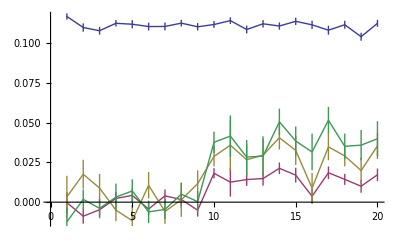
-Graphics-boson_hopping
fermion_hopping_1
fermion_hopping_2
fermion_hopping_3

```mathematica
SetDirectory[NotebookDirectory[]];
<<ArmaBinary`
<<ErrorBarPlots`
EE=ImportArmaBinary["E1_t2.bin"];
EE=Map[Select[#,#[[1]]≠0.&]&,EE,{1}];
Row[{ErrorListPlot[EE,ImageSize->400,Joined->True],Spacer[100],TableForm[Table[Style[observables[[i]],ColorData[1,i]],{i,1,Length[observables]}]]}]
Clear[EE]
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<ArmaBinary`
G=ImportArmaBinary["G.bin"];
sG=ImportArmaBinary["sG.bin"];
<<ErrorBarPlots`
i=4;
Row[{ErrorListPlot[Transpose[{G,sG},{4,1,3,2}][[i]],
Joined->True,ImageSize->400,PlotLabel->observables[[i]],PlotRange->All],
Spacer[100],
TableForm[Table[Style[parameters[[i]],ColorData[1,i]],{i,1,Length[parameters]}]]}]
i=5;
Row[{ErrorListPlot[Transpose[{G,sG},{4,2,3,1}][[i]],
PlotLabel->parameters[[i]],Joined->True,ImageSize->400,PlotRange->All],
Spacer[100],
TableForm[Table[Style[observables[[i]],ColorData[1,i]],{i,1,Length[observables]}]]}]
Clear[G,sG,i]
```